```mathematica
<<peeters` ;
```

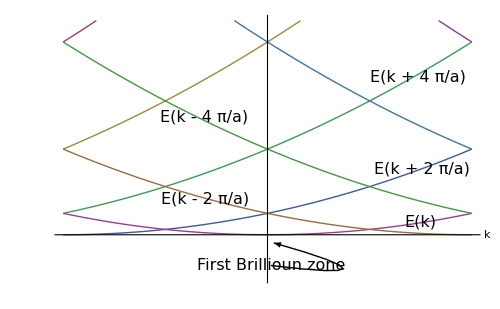
```mathematica
Clear[q]
q = -Graphics-;
```

### Reserve the following expression in your Notebook to restore your Labels and Arrows the next time you need to include them in the Plot

{FeboAsoma,{{0.0314078,-0.38074},{0.714985,-2.24335},{0.016902,-1.43452}},{{0.747192,0.608182},{-0.305962,1.68876},{-0.309183,5.5008},{0.753633,3.0695},{0.734309,7.3618}},{First Brillioun zone},{E(k),E(k - 2 π/a),E(k - 4 π/a),E(k + 2 π/a),E(k + 4 π/a)},FeboAsoma}

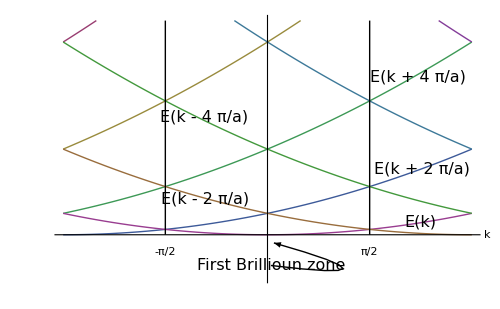

```mathematica
Clear[r]
r = Show[ q, Graphics[Flatten[ Table[{Line[{{m/2, 0}, {m/2, 10}}],Text[m Pi/2,{m /2, -0.8}]},{m, -1, 1, 2}]] ]
]
```

```mathematica
peeters`setGitDir[ "blogit" ]
```

C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit

```mathematica
peeters`exportForLatex["nearlyFreeFig1", r]
```

{C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/nearlyFreeFig1.eps,C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/nearlyFreeFig1pn.png}